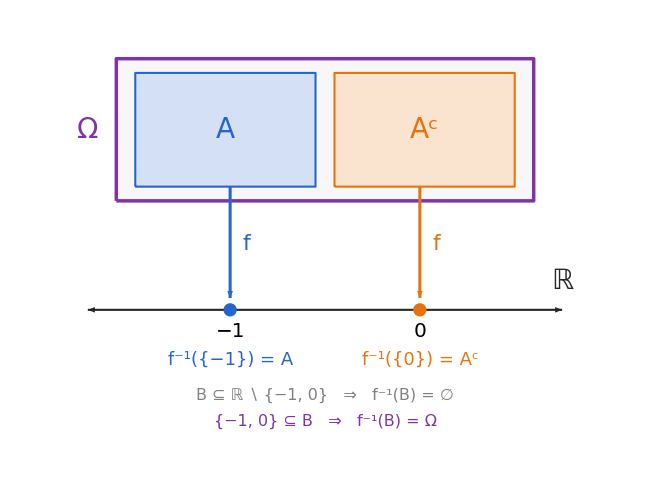

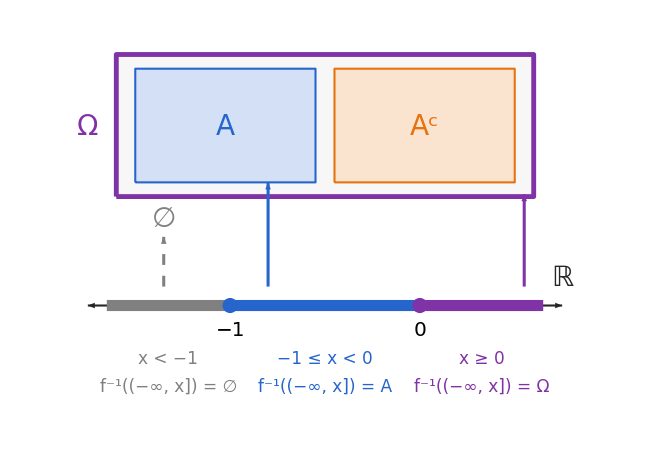

```mathematica
(* ================================================================PROBLEMA 42-Diagramas de apoyo Método 1->T3_P42_a.png        Método 2->T3_P42_b.png================================================================*)(*----------Paleta (coherente entre ambos diagramas)----------*)colA=RGBColor[0.15,0.40,0.80];   (*A:azul*)
colAc=RGBColor[0.90,0.45,0.05];   (*A^c:naranja*)
colOm=RGBColor[0.50,0.20,0.65];   (*Ω:morado*)
colVac=GrayLevel[0.50];              (*∅:gris*)
colEje=GrayLevel[0.15];              (*ejes:casi negro*)

(*----------Utilidades----------*)
txt[e_,pos_,tam_:18,col_:Black]:=Text[Style[e,tam,col,FontFamily->"Times New Roman"],pos];

(*f^{-1}(arg)=res*)
fInv[arg_,res_]:=Row[{Superscript[Style["f",Italic],-1],"(",arg,") = ",res}];

(*f^{-1}((-∞,x])=res*)
fInvInt[res_]:=Row[{Superscript[Style["f",Italic],-1],"((−∞, ",Style["x",Italic],"]) = ",res}];

(*Conjunto de partida Ω con la partición {A,A^c}*)
partida[colBorde_:colOm,grosor_:2.5]:={EdgeForm[{colBorde,AbsoluteThickness[grosor]}],FaceForm[GrayLevel[0.97]],Rectangle[{-4.4,3.2},{4.4,6.2},RoundingRadius->0.4],EdgeForm[{colA,AbsoluteThickness[1.5]}],FaceForm[Lighter[colA,0.8]],Rectangle[{-4.0,3.5},{-0.2,5.9},RoundingRadius->0.3],EdgeForm[{colAc,AbsoluteThickness[1.5]}],FaceForm[Lighter[colAc,0.8]],Rectangle[{0.2,3.5},{4.0,5.9},RoundingRadius->0.3],txt["A",{-2.1,4.7},28,colA],txt[Superscript["A","c"],{2.1,4.7},28,colAc],txt["Ω",{-5.0,4.7},28,colBorde]};

(*Recta real con flechas en ambos extremos*)
recta[]:={colEje,AbsoluteThickness[1.5],Arrowheads[{-0.03,0.03}],Arrow[{{-5,0.9},{5,0.9}}]};


(* ================================================================DIAGRAMA 1 (Método 1):antiimagen de borelianos arbitrarios================================================================*)
diagrama1=Graphics[{partida[],txt["ℝ",{5.0,1.5},28,colEje],recta[],(*puntos-1 y 0 (esquemático,sin escala)*){colA,Disk[{-2,0.9},0.14]},{colAc,Disk[{2,0.9},0.14]},txt["−1",{-2,0.45},20],txt["0",{2,0.45},20],(*flechas de f:A->-1,A^c->0*){AbsoluteThickness[2.2],Arrowheads[0.035],colA,Arrow[{{-2,3.5},{-2,1.15}}],colAc,Arrow[{{2,3.5},{2,1.15}}]},txt[Style["f",Italic],{-1.65,2.3},22,colA],txt[Style["f",Italic],{2.35,2.3},22,colAc],(*antiimágenes de los puntos*)txt[fInv["{−1}","A"],{-2,-0.15},18,colA],txt[fInv["{0}",Superscript["A","c"]],{2,-0.15},18,colAc],(*los otros dos casos:∅ y Ω*)txt[Row[{"B ⊆ ℝ ∖ {−1, 0}   ⇒   ",fInv["B","∅"]}],{0,-0.9},16,colVac],txt[Row[{"{−1, 0} ⊆ B   ⇒   ",fInv["B","Ω"]}],{0,-1.45},16,colOm]},PlotRange->{{-5.6,5.6},{-1.9,6.5}},ImageSize->650,ImagePadding->5];

diagrama1

Export["T3_P42_a.png",diagrama1,Background->None,ImageResolution->300];


(* ================================================================DIAGRAMA 2 (Método 2):antiimagen de las semirrectas (-∞,x]================================================================*)
zona[xc_,cond_,res_,col_]:={txt[cond,{xc,-0.2},17,col],txt[fInvInt[res],{xc,-0.8},17,col]};

diagrama2=Graphics[{partida[colOm,3.5],txt["ℝ",{5.0,1.5},28,colEje],recta[],(*zonas de x coloreadas sobre la recta*){CapForm["Butt"],AbsoluteThickness[8],colVac,Line[{{-4.6,0.9},{-2,0.9}}],colA,Line[{{-2,0.9},{2,0.9}}],colOm,Line[{{2,0.9},{4.6,0.9}}]},(*puntos-1 y 0 (pertenecen al tramo de su derecha)*){colA,Disk[{-2,0.9},0.16]},{colOm,Disk[{2,0.9},0.16]},txt["−1",{-2,0.4},20],txt["0",{2,0.4},20],(*flechas de antiimagen:de cada tramo de R hacia su conjunto en Ω*){AbsoluteThickness[2.2],Arrowheads[0.035],{colVac,Dashing[{0.012,0.012}],Arrow[{{-3.4,1.3},{-3.4,2.35}}]},colA,Arrow[{{-1.2,1.3},{-1.2,3.5}}],colOm,Arrow[{{4.2,1.3},{4.2,3.25}}]},txt["∅",{-3.4,2.75},28,colVac],(*rótulos de cada caso*)zona[-3.3,Row[{Style["x",Italic]," < −1"}],"∅",colVac],zona[0,Row[{"−1 ≤ ",Style["x",Italic]," < 0"}],"A",colA],zona[3.3,Row[{Style["x",Italic]," ≥ 0"}],"Ω",colOm]},PlotRange->{{-5.6,5.6},{-1.3,6.5}},ImageSize->650,ImagePadding->5];

diagrama2

Export["T3_P42_b.png",diagrama2,Background->None,ImageResolution->300];
```

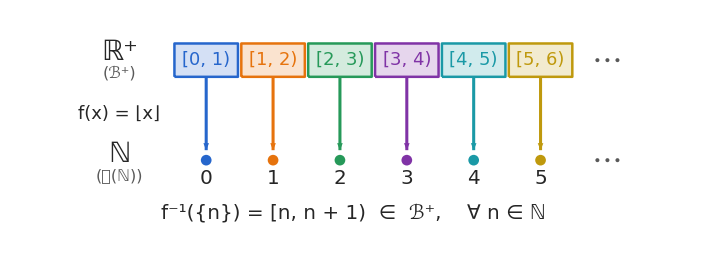

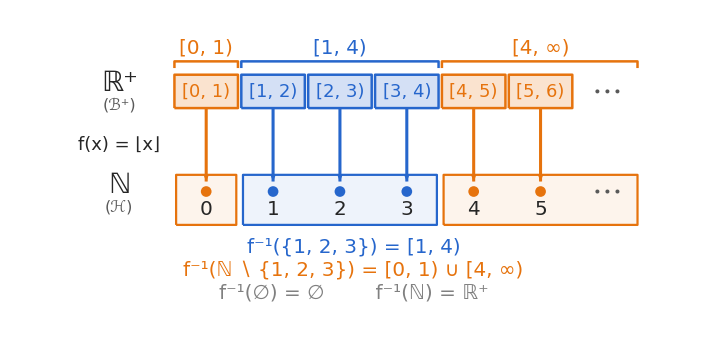

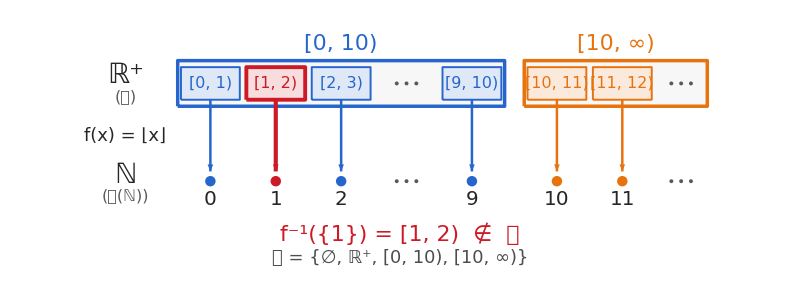

```mathematica
(* ================================================================PROBLEMA 43-Diagramas de apoyo   (nombres únicos,sin colisiones) a)->T3_P43_a.png    b)->T3_P43_b.png    c)->T3_P43_c.png================================================================*)(*----------Colores----------*)c43Azul=RGBColor[0.15,0.40,0.80];   (*azul*)
c43Nar=RGBColor[0.90,0.45,0.05];   (*naranja*)
c43Mor=RGBColor[0.50,0.20,0.65];   (*morado*)
c43Gris=GrayLevel[0.50];              (*gris*)
c43Eje=GrayLevel[0.15];              (*casi negro*)
c43Rojo=RGBColor[0.80,0.10,0.15];   (*rojo:antiimagen NO medible*)

c43Paleta={c43Azul,c43Nar,RGBColor[0.15,0.60,0.35],c43Mor,RGBColor[0.10,0.60,0.65],RGBColor[0.75,0.60,0.05]};

(*----------Utilidades----------*)
t43[e_,pos_,tam_:18,col_:Black]:=Text[Style[e,tam,col,FontFamily->"Times New Roman"],pos];

i43[s_]:=Style[s,Italic];

(*f^{-1}(arg)=res*)
f43[arg_,res_]:=Row[{Superscript[i43["f"],-1],"(",arg,") = ",res}];

(*intervalo[a,b)*)
s43[a_,b_]:=Row[{"[",a,", ",b,")"}];

(*tres puntos suspensivos*)
susp43[x_,y_,col_:GrayLevel[0.35]]:={col,Disk[{x-0.3,y},0.06],Disk[{x,y},0.06],Disk[{x+0.3,y},0.06]};

(*rótulos de las sigma-álgebras*)
sB43=Row[{"(",Superscript["ℬ","+"],")"}];
sPN43=Row[{"(","𝒫","(","ℕ","))"}];
sH43=Row[{"(","ℋ",")"}];
sG43=Row[{"(","𝒢",")"}];

(*etiquetas laterales:espacio de partida (arriba) y de llegada (abajo)*)
etiq43[sigPartida_,sigLlegada_]:={t43[Superscript["ℝ","+"],{-1.6,4.35},28,c43Eje],t43[sigPartida,{-1.6,3.7},16,GrayLevel[0.35]],t43[Row[{i43["f"],"(",i43["x"],") = ⌊",i43["x"],"⌋"}],{-1.6,2.5},18,c43Eje],t43["ℕ",{-1.6,1.3},28,c43Eje],t43[sigLlegada,{-1.6,0.65},16,GrayLevel[0.35]]};

(*Bloque[k,k+1) de la tira superior (centro en x=2k+1)*)
bloq43[k_,col_]:={EdgeForm[{col,AbsoluteThickness[1.8]}],FaceForm[Lighter[col,0.8]],Rectangle[{2 k+0.05,3.6},{2 k+1.95,4.6},RoundingRadius->0.15],t43[s43[k,k+1],{2 k+1,4.1},18,col]};

(*Punto k de N (abajo) y flecha desde su bloque*)
pto43[k_,col_]:={col,Disk[{2 k+1,1.1},0.16],t43[k,{2 k+1,0.55},20,c43Eje]};

flc43[k_,col_]:={col,AbsoluteThickness[2.2],Arrowheads[0.035],Arrow[{{2 k+1,3.6},{2 k+1,1.4}}]};


(* ================================================================DIAGRAMA a):G=B^+ ,H=P(N) Cada singleton {n} tiene antiimagen[n,n+1)================================================================*)
diagA43=Graphics[{Table[bloq43[k,c43Paleta[[k+1]]],{k,0,5}],susp43[13,4.1],susp43[13,1.1],Table[{flc43[k,c43Paleta[[k+1]]],pto43[k,c43Paleta[[k+1]]]},{k,0,5}],etiq43[sB43,sPN43],t43[Row[{f43[Row[{"{",i43["n"],"}"}],s43[i43["n"],Row[{i43["n"]," + 1"}]]],"  ∈  ",Superscript["ℬ","+"],",    ∀ ",i43["n"]," ∈ ℕ"}],{5.4,-0.5},20,c43Eje]},PlotRange->{{-3.2,14.4},{-1.1,5.2}},ImageSize->720,ImagePadding->5];

diagA43

Export["T3_P43_a.png",diagA43,Background->None,ImageResolution->300];


(* ================================================================DIAGRAMA b):G=B^+ ,H={N,∅,{1,2,3},N\ {1,2,3}} Azul={1,2,3};Naranja=N\ {1,2,3}================================================================*)
cB43[k_]:=If[1<=k<=3,c43Azul,c43Nar];

(*llave sobre la tira superior*)
llave43[x1_,x2_,y_,col_]:={col,AbsoluteThickness[1.8],Line[{{x1,y-0.2},{x1,y},{x2,y},{x2,y-0.2}}]};

(*recuadro punteado que agrupa puntos de N*)
grupo43[{x1_,x2_},col_]:={EdgeForm[{col,AbsoluteThickness[1.6],Dashing[{0.012,0.008}]}],FaceForm[Lighter[col,0.92]],Rectangle[{x1,0.1},{x2,1.6},RoundingRadius->0.3]};

diagB43=Graphics[{(*grupos en N (al fondo)*)grupo43[{2.1,7.9},c43Azul],grupo43[{0.1,1.9},c43Nar],grupo43[{8.1,13.9},c43Nar],Table[bloq43[k,cB43[k]],{k,0,5}],susp43[13,4.1],susp43[13,1.1],Table[{flc43[k,cB43[k]],pto43[k,cB43[k]]},{k,0,5}],etiq43[sB43,sH43],(*llaves con las antiimágenes en R^+*)llave43[2.05,7.95,5.0,c43Azul],t43[s43[1,4],{5,5.4},20,c43Azul],llave43[0.05,1.95,5.0,c43Nar],t43[s43[0,1],{1,5.4},20,c43Nar],llave43[8.05,13.9,5.0,c43Nar],t43[s43[4,"∞"],{11,5.4},20,c43Nar],(*los cuatro elementos de H y sus antiimágenes*)t43[f43["{1, 2, 3}",s43[1,4]],{5.4,-0.55},20,c43Azul],t43[f43["ℕ ∖ {1, 2, 3}",Row[{s43[0,1]," ∪ ",s43[4,"∞"]}]],{5.4,-1.25},20,c43Nar],t43[Row[{f43["∅","∅"],"        ",f43["ℕ",Superscript["ℝ","+"]]}],{5.4,-1.95},20,c43Gris]},PlotRange->{{-3.2,14.4},{-2.5,5.9}},ImageSize->720,ImagePadding->5];

diagB43

Export["T3_P43_b.png",diagB43,Background->None,ImageResolution->300];


(* ================================================================DIAGRAMA c):G={∅,R^+,[0,10),[10,∞)},H=P(N) Dibujo esquemático (sin escala).Rojo={1},cuya antiimagen[1,2) "parte" el átomo[0,10) y por tanto no está en G================================================================*)
(*columnas esquemáticas:{k,centro x}*)
colsC43={{0,1},{1,3},{2,5},{9,9},{10,11.6},{11,13.6}};

cK43[k_]:=If[k==1,c43Rojo,If[k<10,c43Azul,c43Nar]];

bloqC43[k_,xc_,col_]:={EdgeForm[{col,AbsoluteThickness[If[k==1,2.8,1.4]]}],FaceForm[Lighter[col,0.85]],Rectangle[{xc-0.9,3.6},{xc+0.9,4.6},RoundingRadius->0.12],t43[s43[k,k+1],{xc,4.1},16,col]};

ptoC43[k_,xc_,col_]:={col,Disk[{xc,1.1},0.16],t43[k,{xc,0.55},20,c43Eje]};

flcC43[xc_,col_]:={col,AbsoluteThickness[If[col===c43Rojo,3,1.8]],Arrowheads[0.035],Arrow[{{xc,3.6},{xc,1.4}}]};

diagC43=Graphics[{(*átomos de G:[0,10) y[10,∞)*){EdgeForm[{c43Azul,AbsoluteThickness[2.5]}],FaceForm[GrayLevel[0.97]],Rectangle[{0,3.4},{10,4.8},RoundingRadius->0.3]},{EdgeForm[{c43Nar,AbsoluteThickness[2.5]}],FaceForm[GrayLevel[0.97]],Rectangle[{10.6,3.4},{16.2,4.8},RoundingRadius->0.3]},t43[s43[0,10],{5,5.3},22,c43Azul],t43[s43[10,"∞"],{13.4,5.3},22,c43Nar],(*subintervalos[k,k+1),puntos de N y flechas*)(bloqC43[#1,#2,cK43[#1]]&)@@@colsC43,(flcC43[#2,cK43[#1]]&)@@@colsC43,(ptoC43[#1,#2,cK43[#1]]&)@@@colsC43,susp43[7,4.1],susp43[7,1.1],susp43[15.4,4.1],susp43[15.4,1.1],etiq43[sG43,sPN43],(*conclusión visual*)t43[Row[{f43["{1}",s43[1,2]],"  ∉  ","𝒢"}],{6.8,-0.5},22,c43Rojo],t43[Row[{"𝒢 = {∅, ",Superscript["ℝ","+"],", ",Style[s43[0,10],c43Azul],", ",Style[s43[10,"∞"],c43Nar],"}"}],{6.8,-1.25},18,GrayLevel[0.3]]},PlotRange->{{-3.2,16.8},{-1.9,5.8}},ImageSize->800,ImagePadding->5];

diagC43

Export["T3_P43_c.png",diagC43,Background->None,ImageResolution->300];
```

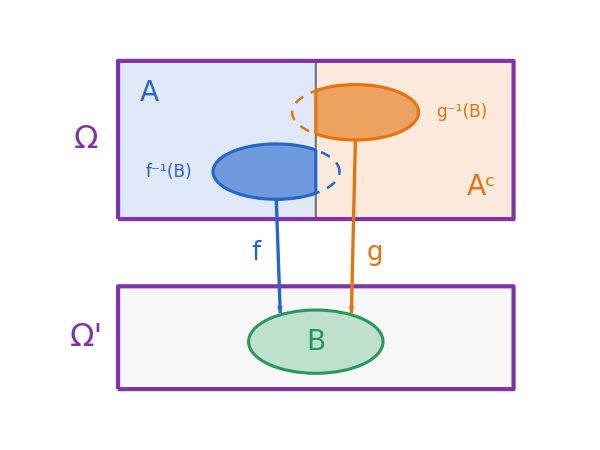

```mathematica
(* ================================================================PROBLEMA 44-Diagrama de apoyo (versión corregida)->T3_P44_a.png (nombres con sufijo 44 para evitar colisiones con otras celdas)================================================================*)(*----------Colores----------*)c44A=RGBColor[0.15,0.40,0.80];   (*azul:A  y  f*)
c44Ac=RGBColor[0.90,0.45,0.05];   (*naranja:A^c y g*)
c44Om=RGBColor[0.50,0.20,0.65];   (*morado:Ω,Ω'*)
c44B=RGBColor[0.15,0.60,0.35];   (*verde:B*)

(*----------Utilidades----------*)
t44[e_,pos_,tam_:18,col_:Black]:=Text[Style[e,tam,col,FontFamily->"Times New Roman"],pos];

(*Ω' con la prima como superíndice*)
omP44=Superscript["Ω","′"];

(*parte de una elipse situada a la izquierda de x=xc*)
izq44[{x0_,y0_},{a_,b_},xc_]:=Module[{t0=ArcCos[(xc-x0)/a]},Polygon[Table[{x0+a Cos[t],y0+b Sin[t]},{t,t0,2 Pi-t0,(2 Pi-2 t0)/80}]]];

(*parte de una elipse situada a la derecha de x=xc*)
der44[{x0_,y0_},{a_,b_},xc_]:=Module[{t1=ArcCos[(xc-x0)/a]},Polygon[Table[{x0+a Cos[t],y0+b Sin[t]},{t,-t1,t1,2 t1/80}]]];

(*antiimágenes completas:f^{-1}(B) (azul) y g^{-1}(B) (naranja)*)
cf44={-1.0,5.2};rf44={1.6,0.7};
cg44={1.0,6.7};rg44={1.6,0.7};


(* ================================================================DIAGRAMA:Ω arriba (A y A^c lo cubren por completo) y Ω' abajo (con B) Línea discontinua=antiimagen completa por f (o g) Zona rellena=la parte que realmente queda en h^{-1}(B)================================================================*)
diagrama44=Graphics[{(*----Espacio de partida Ω=A∪A^c (sin huecos)----*)EdgeForm[None],FaceForm[Lighter[c44A,0.85]],Rectangle[{-5,4},{0,8}],FaceForm[Lighter[c44Ac,0.85]],Rectangle[{0,4},{5,8}],{GrayLevel[0.45],AbsoluteThickness[1.5],Line[{{0,4},{0,8}}]},(*----antiimágenes completas (discontinuas):invaden el otro bloque----*){c44A,AbsoluteThickness[1.8],Dashing[{0.012,0.010}],Circle[cf44,rf44]},{c44Ac,AbsoluteThickness[1.8],Dashing[{0.012,0.010}],Circle[cg44,rg44]},(*----partes que se conservan:f^{-1}(B) en A  y  g^{-1}(B) en A^c----*){EdgeForm[{c44A,AbsoluteThickness[2.2]}],FaceForm[Opacity[0.6,c44A]],izq44[cf44,rf44,0]},{EdgeForm[{c44Ac,AbsoluteThickness[2.2]}],FaceForm[Opacity[0.6,c44Ac]],der44[cg44,rg44,0]},(*----marco exterior de Ω----*){EdgeForm[{c44Om,AbsoluteThickness[3]}],FaceForm[None],Rectangle[{-5,4},{5,8}]},(*----Espacio de llegada Ω' con el suceso B----*)EdgeForm[{c44Om,AbsoluteThickness[3]}],FaceForm[GrayLevel[0.97]],Rectangle[{-5,-0.3},{5,2.3}],EdgeForm[{c44B,AbsoluteThickness[2.2]}],FaceForm[Lighter[c44B,0.7]],Disk[{0,0.9},{1.7,0.8}],(*----flechas:f desde la parte de A,g desde la parte de A^c----*){AbsoluteThickness[2.4],Arrowheads[0.035],c44A,Arrow[{{-1.0,4.5},{-0.9,1.62}}],c44Ac,Arrow[{{1.0,6.0},{0.9,1.62}}]},t44[Style["f",Italic],{-1.5,3.15},26,c44A],t44[Style["g",Italic],{1.5,3.15},26,c44Ac],(*----rótulos----*)t44["Ω",{-5.8,6.0},32,c44Om],t44[omP44,{-5.8,1.0},32,c44Om],t44["A",{-4.2,7.2},28,c44A],t44[Superscript["A","c"],{4.2,4.8},28,c44Ac],t44["B",{0.0,0.9},28,c44B],t44[Row[{Superscript[Style["f",Italic],"−1"],"(B)"}],{-3.7,5.2},17,c44A],t44[Row[{Superscript[Style["g",Italic],"−1"],"(B)"}],{3.7,6.7},17,c44Ac]},PlotRange->{{-6.6,5.8},{-0.8,8.5}},ImageSize->600,ImagePadding->5];

diagrama44

Export["T3_P44_a.png",diagrama44,Background->None,ImageResolution->300];
```

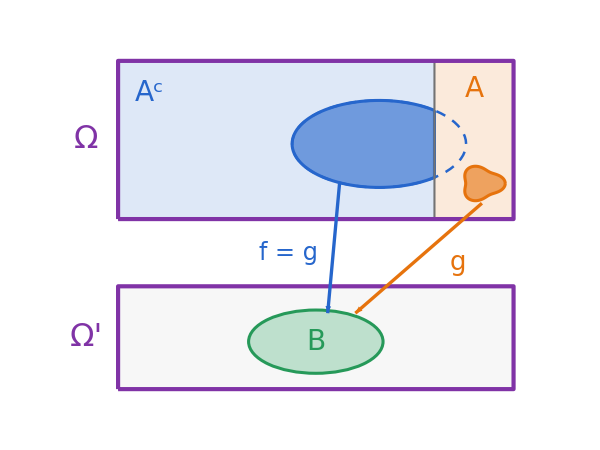

```mathematica
(* ================================================================PROBLEMA 45-Diagrama de apoyo->T3_P45_a.png (nombres con sufijo 45 para evitar colisiones con otras celdas)================================================================*)(*----------Colores----------*)c45Ac=RGBColor[0.15,0.40,0.80];   (*azul:A^c (donde g=f)*)
c45A=RGBColor[0.90,0.45,0.05];   (*naranja:A  (medida nula)*)
c45Om=RGBColor[0.50,0.20,0.65];   (*morado:Ω,Ω'*)
c45B=RGBColor[0.15,0.60,0.35];   (*verde:B*)

(*----------Utilidades----------*)
t45[e_,pos_,tam_:18,col_:Black]:=Text[Style[e,tam,col,FontFamily->"Times New Roman"],pos];

(*Ω' con la prima como superíndice*)
omP45=Superscript["Ω","′"];

(*frontera vertical entre A^c (izquierda) y A (derecha)*)
xc45=3;

(*parte de una elipse situada a la izquierda de x=xc*)
izq45[{x0_,y0_},{a_,b_},xc_]:=Module[{t0=ArcCos[(xc-x0)/a]},Polygon[Table[{x0+a Cos[t],y0+b Sin[t]},{t,t0,2 Pi-t0,(2 Pi-2 t0)/80}]]];

(*mancha irregular:simboliza un subconjunto cualquiera de A*)
mancha45[{x0_,y0_},{a_,b_}]:=Polygon[Table[{x0+a (1+0.18 Cos[3 t]) Cos[t],y0+b (1+0.18 Cos[3 t]) Sin[t]},{t,0,2 Pi,2 Pi/100}]];

(*f^{-1}(B) completa (elipse discontinua) y g^{-1}(B)∩A (mancha)*)
cf45={1.6,5.9};rf45={2.2,1.1};
cm45={4.2,4.9};rm45={0.5,0.4};


(* ================================================================DIAGRAMA:Ω arriba (A^c grande+A pequeño,sin huecos) y Ω' abajo (con B) Zona azul rellena=f^{-1}(B)∩A^c   (aquí g=f) Mancha naranja=g^{-1}(B)∩A     (subconjunto cualquiera de A) Elipse discontinua=f^{-1}(B) completa;su trozo dentro de A se descarta================================================================*)
diagrama45=Graphics[{(*----Espacio de partida Ω=A^c∪A (sin huecos)----*){EdgeForm[None],FaceForm[Lighter[c45Ac,0.85]],Rectangle[{-5,4},{xc45,8}],FaceForm[Lighter[c45A,0.85]],Rectangle[{xc45,4},{5,8}]},(*----f^{-1}(B) completa (discontinua):invade A----*){c45Ac,AbsoluteThickness[1.8],Dashing[{0.012,0.010}],Circle[cf45,rf45]},(*----parte que se conserva en A^c----*){EdgeForm[{c45Ac,AbsoluteThickness[2.2]}],FaceForm[Opacity[0.6,c45Ac]],izq45[cf45,rf45,xc45]},(*----mancha en A----*){EdgeForm[{c45A,AbsoluteThickness[2.2]}],FaceForm[Opacity[0.6,c45A]],mancha45[cm45,rm45]},(*----frontera entre A^c y A----*){GrayLevel[0.45],AbsoluteThickness[1.5],Line[{{xc45,4},{xc45,8}}]},(*----marco exterior de Ω----*){EdgeForm[{c45Om,AbsoluteThickness[3]}],FaceForm[None],Rectangle[{-5,4},{5,8}]},(*----Espacio de llegada Ω' con el suceso B----*){EdgeForm[{c45Om,AbsoluteThickness[3]}],FaceForm[GrayLevel[0.97]],Rectangle[{-5,-0.3},{5,2.3}]},{EdgeForm[{c45B,AbsoluteThickness[2.2]}],FaceForm[Lighter[c45B,0.7]],Disk[{0,0.9},{1.7,0.8}]},(*----flechas:desde la zona de A^c (f=g) y desde A (solo g)----*){AbsoluteThickness[2.4],Arrowheads[0.035],c45Ac,Arrow[{{0.6,4.9},{0.3,1.62}}],c45A,Arrow[{{4.2,4.4},{1.0,1.62}}]},t45[Row[{Style["f",Italic]," = ",Style["g",Italic]}],{-0.7,3.15},24,c45Ac],t45[Style["g",Italic],{3.6,2.9},26,c45A],(*----rótulos----*)t45["Ω",{-5.8,6.0},32,c45Om],t45[omP45,{-5.8,1.0},32,c45Om],t45[Superscript["A","c"],{-4.2,7.2},28,c45Ac],t45["A",{4.0,7.3},28,c45A],t45["B",{0.0,0.9},28,c45B]},PlotRange->{{-6.6,5.8},{-0.8,8.5}},ImageSize->600,ImagePadding->5];

diagrama45

Export["T3_P45_a.png",diagrama45,Background->None,ImageResolution->300];
```

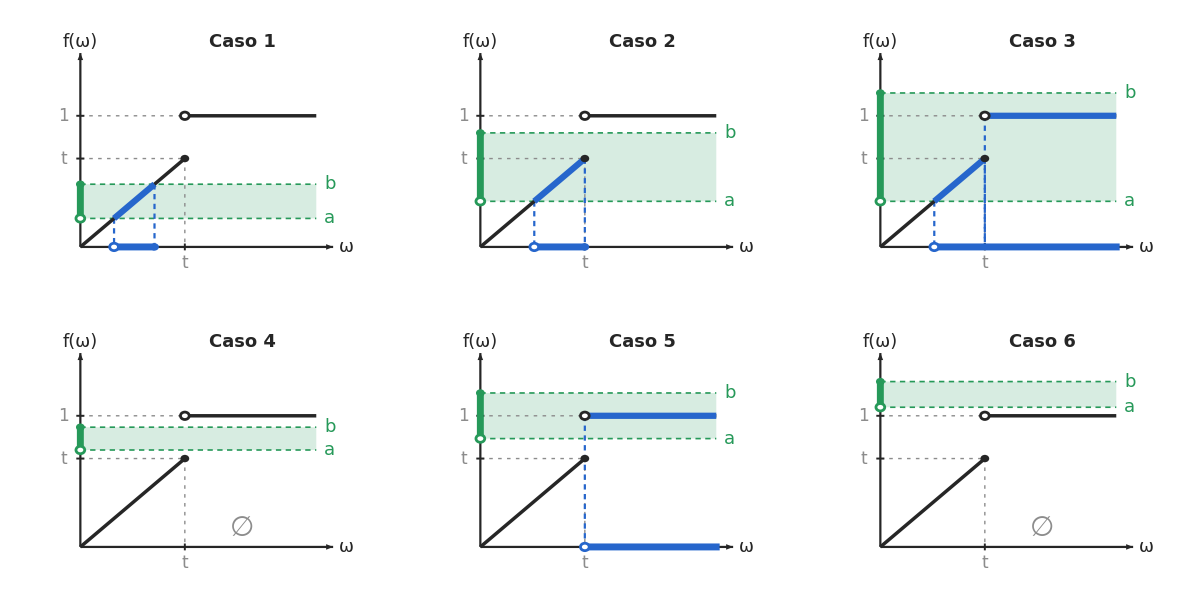

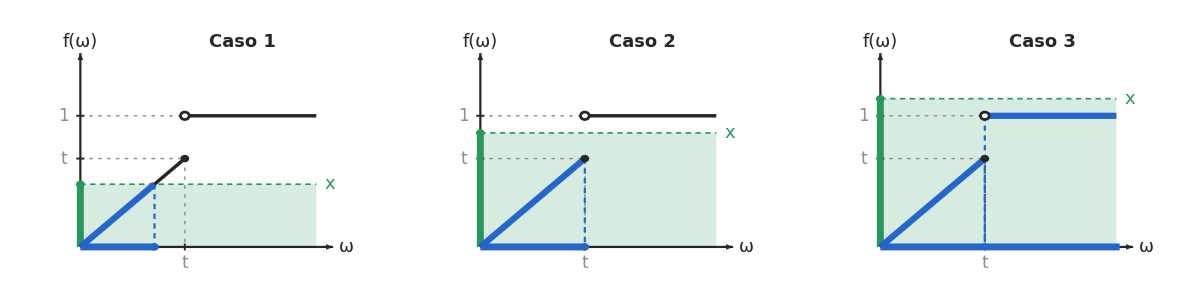

```mathematica
(* ================================================================PROBLEMA 46-Diagramas de apoyo a)->T3_P46_a.png      b)->T3_P46_b.png (nombres con sufijo 46 para evitar colisiones con otras celdas)================================================================*)(*----------Colores----------*)c46B=RGBColor[0.15,0.60,0.35];   (*verde:intervalo en el espacio de llegada*)
c46A=RGBColor[0.15,0.40,0.80];   (*azul:antiimagen en el espacio de partida*)
c46Gr=GrayLevel[0.55];              (*gris:guías y conjunto vacío*)
c46Eje=GrayLevel[0.15];              (*casi negro:ejes y gráfica de f*)

(*----------Geometría (esquemática)----------*)
tt46=-0.5;                  (*valor de t (<1)*)
x046=-3.6;y046=-3.6;    (*esquina donde se cruzan los ejes*)
xa46=3.9;ya46=3.2;     (*extremos (con flecha) de los ejes*)
xg46=3.4;                   (*extremo derecho de la gráfica y la banda*)
xe46=3.5;                   (*extremo derecho del resaltado en el eje x*)
r46=0.13;                  (*radio de los puntos*)

(*----------Utilidades----------*)
t46[e_,pos_,tam_:16,col_:Black]:=Text[Style[e,tam,col,FontFamily->"Times New Roman"],pos];

i46[s_]:=Style[s,Italic];

pAbierto46[pos_,col_]:={EdgeForm[{col,AbsoluteThickness[2]}],FaceForm[White],Disk[pos,r46]};

pCerrado46[pos_,col_]:={EdgeForm[None],FaceForm[col],Disk[pos,r46]};


(* ================================================================PANEL GENÉRICO {a,b}:extremos del intervalo del espacio de llegada (a puede ser-∞) {labA,labB}:rótulos de esos extremos segX:tramos que forman la antiimagen en el eje x abiertos/cerrados:posiciones x de los puntos (abierto/cerrado) de la antiimagen vacio:True si la antiimagen es ∅================================================================*)
panel46[{a_,b_},{labA_,labB_},segX_,abiertos_,cerrados_,vacio_,titulo_]:=Module[{aFin,lo,hi,difHi,horHi,pts},aFin=a>-Infinity;
lo=Max[a,x046];
hi=Min[b,tt46];
(*trozo de la diagonal y trozo horizontal que caen dentro de la banda*)difHi=If[lo<hi,{Line[{{lo,lo},{hi,hi}}]},{}];
horHi=If[a<1&&1<=b,{Line[{{tt46,1},{xg46,1}}]},{}];
(*puntos de la gráfica desde los que se proyecta hacia el eje x*)pts=Join[If[lo<hi,{{hi,hi}},{}],If[lo<hi&&lo>x046,{{lo,lo}},{}],If[a<1&&1<=b,{{tt46,1}},{}]];
Graphics[{(*----banda horizontal:el intervalo del espacio de llegada----*){EdgeForm[None],FaceForm[Opacity[0.18,c46B]],Rectangle[{x046,Max[a,y046]},{xg46,b}]},{c46B,AbsoluteThickness[1.2],Dashing[{0.012,0.010}],If[aFin,Line[{{x046,a},{xg46,a}}],{}],Line[{{x046,b},{xg46,b}}]},(*----guías grises:t y 1----*){c46Gr,AbsoluteThickness[1],Dashing[{0.008,0.012}],Line[{{x046,tt46},{tt46,tt46}}],Line[{{tt46,tt46},{tt46,y046}}],Line[{{x046,1},{tt46,1}}]},(*----proyecciones hacia el eje x----*){c46A,AbsoluteThickness[1.6],Dashing[{0.012,0.010}],(Line[{#,{First[#],y046}}]&)/@pts},(*----ejes y marcas----*){c46Eje,AbsoluteThickness[1.6],Arrowheads[0.04],Arrow[{{x046,y046},{xa46,y046}}],Arrow[{{x046,y046},{x046,ya46}}]},{c46Eje,AbsoluteThickness[1.4],Line[{{x046-0.12,tt46},{x046+0.12,tt46}}],Line[{{x046-0.12,1},{x046+0.12,1}}],Line[{{tt46,y046-0.12},{tt46,y046+0.12}}]},(*----resaltado sobre los ejes:intervalo (verde) y antiimagen (azul)----*){c46B,AbsoluteThickness[5],CapForm["Butt"],Line[{{x046,Max[a,y046]},{x046,b}}]},{c46A,AbsoluteThickness[5],CapForm["Butt"],(Line[{{#1,y046},{#2,y046}}]&)@@@segX},(*----gráfica de f y trozo que cae dentro de la banda----*){c46Eje,AbsoluteThickness[2.5],Line[{{x046,x046},{tt46,tt46}}],Line[{{tt46,1},{xg46,1}}]},{c46A,AbsoluteThickness[4.5],CapForm["Butt"],difHi,horHi},(*----puntos abiertos/cerrados----*)If[aFin,pAbierto46[{x046,a},c46B],{}],pCerrado46[{x046,b},c46B],(pAbierto46[{#,y046},c46A]&)/@abiertos,(pCerrado46[{#,y046},c46A]&)/@cerrados,pCerrado46[{tt46,tt46},c46Eje],pAbierto46[{tt46,1},c46Eje],(*----conjunto vacío----*)If[vacio,t46["∅",{1.2,y046+0.65},28,c46Gr],{}],(*----rótulos----*)t46[i46["t"],{x046-0.5,tt46},17,c46Gr],t46["1",{x046-0.5,1},17,c46Gr],t46[i46["t"],{tt46,y046-0.55},17,c46Gr],If[aFin,t46[labA,{xa46-0.1,a},18,c46B],{}],t46[labB,{xa46-0.1,b},18,c46B],t46[i46["ω"],{xa46+0.4,y046},18,c46Eje],t46[Row[{i46["f"],"(",i46["ω"],")"}],{x046,ya46+0.4},18,c46Eje],t46[Style[titulo,Bold],{1.2,3.6},18,c46Eje]},PlotRange->{{-4.9,4.8},{-4.5,4.1}},PlotRangePadding->None,ImageSize->320,ImagePadding->3]];


(* ================================================================DIAGRAMA a):intervalos (a,b]->los 6 casos del enunciado================================================================*)
panelesA46={panel46[{-2.6,-1.4},{i46["a"],i46["b"]},{{-2.6,-1.4}},{-2.6},{-1.4},False,"Caso 1"],panel46[{-2.0,0.4},{i46["a"],i46["b"]},{{-2.0,tt46}},{-2.0},{tt46},False,"Caso 2"],panel46[{-2.0,1.8},{i46["a"],i46["b"]},{{-2.0,xe46}},{-2.0},{},False,"Caso 3"],panel46[{-0.2,0.6},{i46["a"],i46["b"]},{},{},{},True,"Caso 4"],panel46[{0.2,1.8},{i46["a"],i46["b"]},{{tt46,xe46}},{tt46},{},False,"Caso 5"],panel46[{1.3,2.2},{i46["a"],i46["b"]},{},{},{},True,"Caso 6"]};

diagA46=Grid[Partition[panelesA46,3],Spacings->{1,1}];

diagA46

Export["T3_P46_a.png",diagA46,Background->None,ImageResolution->300];


(* ================================================================DIAGRAMA b):semirrectas (-∞,x]->los 3 casos del enunciado================================================================*)
panelesB46={panel46[{-Infinity,-1.4},{"",i46["x"]},{{x046,-1.4}},{},{-1.4},False,"Caso 1"],panel46[{-Infinity,0.4},{"",i46["x"]},{{x046,tt46}},{},{tt46},False,"Caso 2"],panel46[{-Infinity,1.6},{"",i46["x"]},{{x046,xe46}},{},{},False,"Caso 3"]};

diagB46=Grid[{panelesB46},Spacings->{1,1}];

diagB46

Export["T3_P46_b.png",diagB46,Background->None,ImageResolution->300];
```

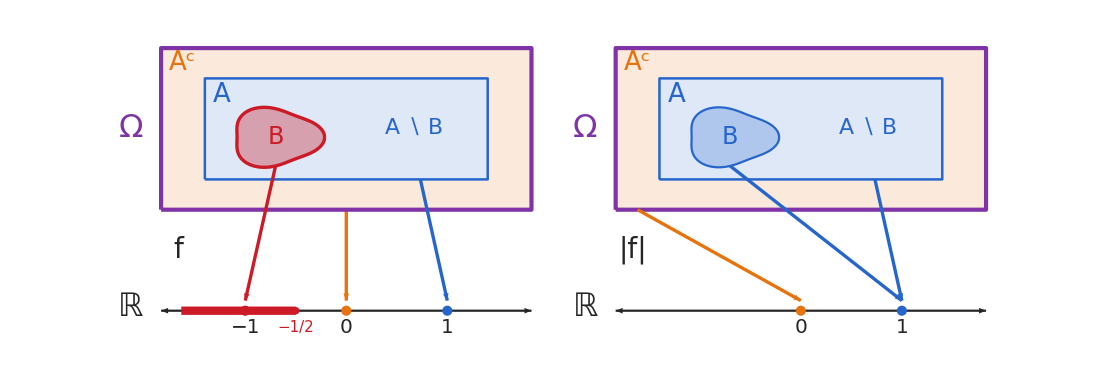

```mathematica
(* ================================================================PROBLEMA 47-Diagrama de apoyo->T3_P47_a.png Izquierda:f|Derecha: |f|(nombres con sufijo 47 para evitar colisiones con otras celdas)================================================================*)(*----------Colores----------*)c47A=RGBColor[0.15,0.40,0.80];   (*azul:A*)
c47Ac=RGBColor[0.90,0.45,0.05];   (*naranja:A^c*)
c47Om=RGBColor[0.50,0.20,0.65];   (*morado:Ω*)
c47B=RGBColor[0.80,0.10,0.15];   (*rojo:B (no medible)*)
c47Eje=GrayLevel[0.15];              (*casi negro:ejes*)

(*----------Utilidades----------*)
t47[e_,pos_,tam_:18,col_:Black]:=Text[Style[e,tam,col,FontFamily->"Times New Roman"],pos];

i47[s_]:=Style[s,Italic];

(*mancha irregular:simboliza un subconjunto cualquiera*)
blob47[{x0_,y0_},{a_,b_}]:=Polygon[Table[{x0+a (1+0.12 Cos[3 s]) Cos[s],y0+b (1+0.12 Cos[3 s]) Sin[s]},{s,0,2 Pi,2 Pi/100}]];


(* ================================================================PANEL:dx desplaza el panel en horizontal modo "f":B->-1,A\B->1,A^c->0 modo "abs":B->1,A\B->1,A^c->0 Distribución de Ω:A^c de fondo,A dentro,B dentro de A (así ninguna flecha se cruza con otra)================================================================*)
panel47[dx_,modo_]:=Module[{q,esF},q[x_,y_]:={dx+x,y};
esF=(modo==="f");
{(*----Ω:A^c de fondo,A dentro,B dentro de A----*){EdgeForm[None],FaceForm[Lighter[c47Ac,0.85]],Rectangle[q[-5.5,3.9],q[5.5,8.7]]},{EdgeForm[{c47A,AbsoluteThickness[1.8]}],FaceForm[Lighter[c47A,0.85]],Rectangle[q[-4.2,4.8],q[4.2,7.8],RoundingRadius->0.3]},If[esF,{EdgeForm[{c47B,AbsoluteThickness[2.4]}],FaceForm[Opacity[0.35,c47B]],blob47[q[-2.1,6.05],{1.3,0.85}]},{EdgeForm[{c47A,AbsoluteThickness[1.6],Dashing[{0.010,0.008}]}],FaceForm[Opacity[0.25,c47A]],blob47[q[-2.1,6.05],{1.3,0.85}]}],{EdgeForm[{c47Om,AbsoluteThickness[3]}],FaceForm[None],Rectangle[q[-5.5,3.9],q[5.5,8.7]]},(*----recta real----*){c47Eje,AbsoluteThickness[1.6],Arrowheads[{-0.015,0.015}],Arrow[{q[-5.5,0.9],q[5.5,0.9]}]},(*semirrecta (-∞,-1/2],cuya antiimagen es B (solo en f)*)If[esF,{{c47B,AbsoluteThickness[6],CapForm["Butt"],Line[{q[-4.9,0.9],q[-1.5,0.9]}]},{c47B,Disk[q[-1.5,0.9],0.11]},t47["−1/2",q[-1.5,0.4],15,c47B]},{}],(*----puntos de la recta----*)If[esF,{{c47B,Disk[q[-3,0.9],0.15]},t47["−1",q[-3,0.4],20,c47Eje]},{}],{c47Ac,Disk[q[0,0.9],0.15]},t47["0",q[0,0.4],20,c47Eje],{c47A,Disk[q[3,0.9],0.15]},t47["1",q[3,0.4],20,c47Eje],(*----flechas----*){AbsoluteThickness[2.4],Arrowheads[0.02],If[esF,{c47B,Arrow[{q[-2.1,5.2],q[-3,1.2]}],c47A,Arrow[{q[2.2,4.8],q[3,1.2]}],c47Ac,Arrow[{q[0,3.9],q[0,1.2]}]},{c47A,Arrow[{q[-2.1,5.2],q[3,1.2]}],Arrow[{q[2.2,4.8],q[3,1.2]}],c47Ac,Arrow[{q[-4.85,3.9],q[0,1.2]}]}]},t47[If[esF,i47["f"],Row[{"|",i47["f"],"|"}]],q[-5.0,2.7],28,c47Eje],(*----rótulos----*)t47["Ω",q[-6.4,6.3],32,c47Om],t47["ℝ",q[-6.4,1.0],32,c47Eje],t47["A",q[-3.7,7.3],26,c47A],t47[Superscript["A","c"],q[-4.85,8.25],26,c47Ac],t47["B",q[-2.1,6.05],24,If[esF,c47B,c47A]],t47["A ∖ B",q[2.0,6.3],22,c47A]}];


(* ================================================================DIAGRAMA:f (izquierda) y|f|(derecha) Rojo=B,cuya antiimagen no está en la σ-álgebra En|f|,B y A\B llegan al mismo punto (1):B desaparece como suceso distinguible================================================================*)
diagrama47=Graphics[{panel47[0,"f"],panel47[13.5,"abs"]},PlotRange->{{-7.3,19.4},{-0.1,9.1}},ImageSize->1100,ImagePadding->5];

diagrama47

Export["T3_P47_a.png",diagrama47,Background->None,ImageResolution->300];
```

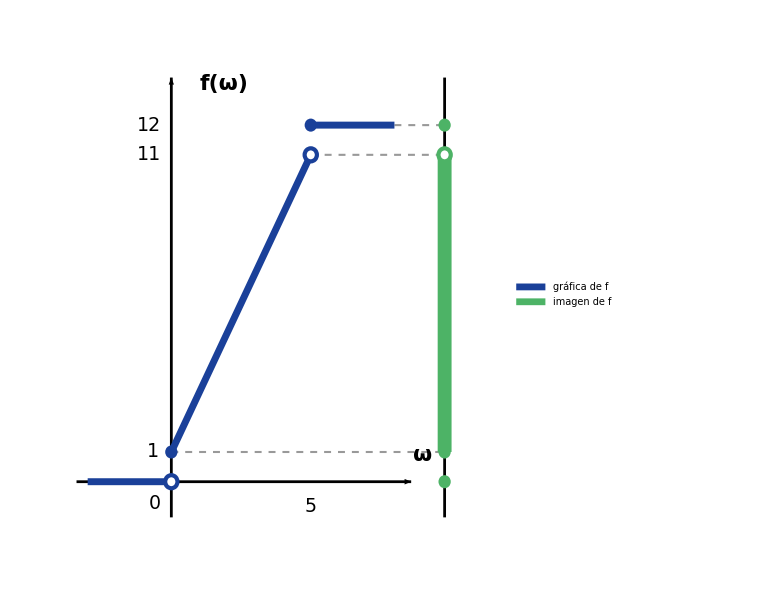

```mathematica
ClearAll[colF,colIm,r,xC,cerrado,abierto,ejes,trozos,guias,ejeCod,etiquetas,grafico1,diagrama1];

colF=RGBColor[0.1,0.25,0.6];     (*gráfica de f*)
colIm=RGBColor[0.3,0.7,0.4];     (*imagen de f*)
r=0.22;
xC=9.8;                            (*recta del codominio,a la derecha*)

cerrado[p_,col_]:={col,Disk[p,r]};
abierto[p_,col_]:={White,Disk[p,r],col,AbsoluteThickness[3],Circle[p,r]};

ejes={Black,AbsoluteThickness[2],Arrowheads[0.025],Arrow[{{-3.4,0},{8.6,0}}],Arrow[{{0,-1.2},{0,13.6}}]};

(*f=0 si ω<0;f=2ω+1 si 0≤ω<5;f=12 si ω≥5*)
trozos={colF,AbsoluteThickness[5],Line[{{-3,0},{0,0}}],Line[{{0,1},{5,11}}],Line[{{5,12},{8,12}}],abierto[{0,0},colF],cerrado[{0,1},colF],abierto[{5,11},colF],cerrado[{5,12},colF]};

guias={GrayLevel[0.6],Dashed,AbsoluteThickness[1.5],Line[{{0,1},{xC,1}}],Line[{{5,11},{xC,11}}],Line[{{8,12},{xC,12}}]};

(*imagen de f={0} ∪[1,11) ∪ {12}*)
ejeCod={Black,AbsoluteThickness[2],Line[{{xC,-1.2},{xC,13.6}}],colIm,AbsoluteThickness[10],CapForm["Butt"],Line[{{xC,1},{xC,11}}],cerrado[{xC,0},colIm],cerrado[{xC,1},colIm],abierto[{xC,11},colIm],cerrado[{xC,12},colIm]};

etiquetas={Black,Text[Style["0",19],{-0.6,-0.75}],Text[Style["5",19],{5,-0.85}],Text[Style["1",19],{-0.65,1}],Text[Style["11",19],{-0.8,11}],Text[Style["12",19],{-0.8,12}],Text[Style["ω",22,Bold],{9.0,0.9}],Text[Style["f(ω)",22,Bold],{1.9,13.4}]};

grafico1=Graphics[{guias,ejes,trozos,ejeCod,etiquetas},PlotRange->{{-3.8,11.6},{-1.8,14.4}},ImageSize->560];

diagrama1=Legended[grafico1,SwatchLegend[{colF,colIm},{"gráfica de f","imagen de f"},LabelStyle->Directive[FontSize->18],LegendMarkerSize->20]];

diagrama1

Export["T2_P49_funcion.png",diagrama1,Background->None,ImageResolution->600];
```

```mathematica
ClearAll[xL,xR,yTop,yBot,colO,colN,rr,cerrado,abierto,trianIzq,trianDer,baseArriba,baseAbajo,guias,segTop,intervaloAbajo,leyenda,caso,diagramas];

xL=-4.5;xR=16.5;     (*extremos visibles de las dos rectas*)
yTop=3.4;yBot=0;     (*altura de R (arriba) y de[0,12] (abajo)*)
colO=RGBColor[0.2,0.55,0.85];    (*antiimagen,en R*)
colN=RGBColor[0.95,0.6,0.15];    (*intervalo (a,b] en el espacio de llegada*)
rr=0.17;

cerrado[p_,col_]:={col,Disk[p,rr]};
abierto[p_,col_]:={White,Disk[p,rr],col,AbsoluteThickness[3],Circle[p,rr]};

trianIzq[col_]:={col,Polygon[{{xL,yTop+0.28},{xL,yTop-0.28},{xL-0.55,yTop}}]};
trianDer[col_]:={col,Polygon[{{xR,yTop+0.28},{xR,yTop-0.28},{xR+0.55,yTop}}]};

(*La recta de arriba usa la escala x=2w+1:el tramo afin 2w+1 se une con lineas verticales.Marcas de arriba:w=0 en x=1 y w=5 en x=11*)
baseArriba={{Black,AbsoluteThickness[2.5],Line[{{xL,yTop},{xR,yTop}}]},trianIzq[Black],trianDer[Black],Table[{Black,AbsoluteThickness[2.5],Line[{{p[[1]],yTop-0.18},{p[[1]],yTop+0.18}}],Text[Style[p[[2]],18],{p[[1]],yTop+0.7}]},{p,{{1,"0"},{11,"5"}}}],Text[Style["ℝ",30,Bold],{xL-1.5,yTop}]};

(*[0,12] en trazo grueso;lo que queda fuera,en gris discontinuo*)
baseAbajo={{GrayLevel[0.7],Dashed,AbsoluteThickness[2],Line[{{xL,yBot},{0,yBot}}],Line[{{12,yBot},{xR,yBot}}]},{Black,AbsoluteThickness[4],Line[{{0,yBot},{12,yBot}}]},Table[{Black,AbsoluteThickness[2.5],Line[{{t,yBot-0.18},{t,yBot+0.18}}],Text[Style[t,18],{t,yBot-0.65}]},{t,{0,1,11,12}}],Text[Style["[0,12]",26,Bold],{6,yBot-2.2}]};

guias={GrayLevel[0.8],Dotted,AbsoluteThickness[1.5],Line[{{1,yTop},{1,yBot}}],Line[{{11,yTop},{11,yBot}}]};

(*tramo de la antiimagen en R:{x1,cerrado1,x2,cerrado2};+-Infinity dibuja flecha*)
segTop[{x1_,c1_,x2_,c2_}]:=Module[{p1=If[x1===-Infinity,xL,x1],p2=If[x2===Infinity,xR,x2]},{colO,AbsoluteThickness[9],CapForm["Butt"],Line[{{p1,yTop},{p2,yTop}}],If[x1===-Infinity,trianIzq[colO],If[c1,cerrado[{p1,yTop},colO],abierto[{p1,yTop},colO]]],If[x2===Infinity,trianDer[colO],If[c2,cerrado[{p2,yTop},colO],abierto[{p2,yTop},colO]]]}];

(*(a,b] completo en tono claro;su traza sobre[0,12] en tono fuerte*)
intervaloAbajo[a_,b_]:=Module[{lo=Max[a,0],hi=Min[b,12]},{{colN,Opacity[0.35],AbsoluteThickness[9],CapForm["Butt"],Line[{{a,yBot},{b,yBot}}]},If[lo<=hi,{colN,AbsoluteThickness[9],CapForm["Butt"],Line[{{lo,yBot},{hi,yBot}}]},{}],abierto[{a,yBot},colN],cerrado[{b,yBot},colN],Text[Style["a",22,Bold,Darker[colN,0.3]],{a,yBot-1.35}],Text[Style["b",22,Bold,Darker[colN,0.3]],{b,yBot-1.35}]}];

leyenda=SwatchLegend[{colO,colN},{"antiimagen","intervalo (a,b]"},LabelStyle->Directive[FontSize->18],LegendMarkerSize->20];

(*fanL:abanico hacia el punto 0 (w<0);mSeg:extremos de las lineas verticales (tramo afin);
fanR:abanico hacia el punto 12 (w>=5);topSegs:antiimagen dibujada en R*)
caso[a_,b_,fanL_,mSeg_,fanR_,topSegs_]:=Legended[Graphics[{guias,baseArriba,baseAbajo,If[fanL,{colO,Opacity[0.12],Polygon[{{xL,yTop},{1,yTop},{0,yBot}}]},{}],If[mSeg=!=None,{colO,Opacity[0.12],Polygon[{{mSeg[[1]],yTop},{mSeg[[2]],yTop},{mSeg[[2]],yBot},{mSeg[[1]],yBot}}]},{}],If[fanR,{colO,Opacity[0.12],Polygon[{{11,yTop},{xR,yTop},{12,yBot}}]},{}],{colO,AbsoluteThickness[2.5],If[fanL,Table[Line[{{u,yTop},{0,yBot}}],{u,{-3.7,-2.2,-0.7,1}}],{}],If[mSeg=!=None,{Line[{{mSeg[[1]],yTop},{mSeg[[1]],yBot}}],Line[{{mSeg[[2]],yTop},{mSeg[[2]],yBot}}]},{}],If[fanR,Table[Line[{{u,yTop},{12,yBot}}],{u,{11,12.6,14.2,15.8}}],{}]},Table[segTop[s],{s,topSegs}],If[topSegs==={},Text[Style["∅",36,Bold,GrayLevel[0.45]],{6,yTop+0.9}],{}],intervaloAbajo[a,b]},PlotRange->{{xL-3,xR+1.2},{yBot-2.8,yTop+1.5}},ImageSize->1000],leyenda];

(*----------------los 15 casos (valores de a y b elegidos como ejemplo)----------------*)
(*a<0*)
diagrama01=caso[-3,-1,False,None,False,{}];                                           (*b<0*)
diagrama02=caso[-2,0.5,True,None,False,{{-Infinity,False,1,False}}];               (*0<=b<1*)
diagrama03=caso[-2,6,True,{1,6},False,{{-Infinity,False,6,True}}];                (*1<=b<11*)
diagrama04=caso[-2,11.5,True,{1,11},False,{{-Infinity,False,11,False}}];          (*11<=b<12*)
diagrama05=caso[-2,13,True,{1,11},True,{{-Infinity,False,Infinity,False}}];       (*b>=12*)
(*0<=a<1*)
diagrama06=caso[0.2,0.7,False,None,False,{}];                                         (*b<1*)
diagrama07=caso[0.4,6,False,{1,6},False,{{1,True,6,True}}];                       (*1<=b<11*)
diagrama08=caso[0.4,11.5,False,{1,11},False,{{1,True,11,False}}];                 (*11<=b<12*)
diagrama09=caso[0.4,13,False,{1,11},True,{{1,True,Infinity,False}}];              (*b>=12*)
(*1<=a<11*)
diagrama10=caso[3,8,False,{3,8},False,{{3,False,8,True}}];                        (*b<11*)
diagrama11=caso[3,11.5,False,{3,11},False,{{3,False,11,False}}];                  (*11<=b<12*)
diagrama12=caso[3,13,False,{3,11},True,{{3,False,Infinity,False}}];               (*b>=12*)
(*a>=11*)
diagrama13=caso[11.3,11.8,False,None,False,{}];                                       (*a<b<12*)
diagrama14=caso[11.3,13,False,None,True,{{11,True,Infinity,False}}];               (*a<12<=b*)
diagrama15=caso[12.5,14.5,False,None,False,{}];                                       (*a>=12*)

diagramas={diagrama01,diagrama02,diagrama03,diagrama04,diagrama05,diagrama06,diagrama07,diagrama08,diagrama09,diagrama10,diagrama11,diagrama12,diagrama13,diagrama14,diagrama15};

(*se guardan como T2_P49_c01.png,...,T2_P49_c15.png*)
Do[Export["T2_P49_c"<>IntegerString[k,10,2]<>".png",diagramas[[k]],Background->None,ImageResolution->600],{k,1,15}];
```